```mathematica
<<MaTeX`
```

```mathematica
data=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi.csv"];
```

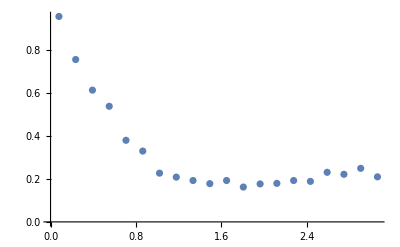

```mathematica
ListPlot[data]
```

```mathematica
Total[data[[All,2]]*ArrayPad[Differences[data[[All,1]]],{0,1},"Reversed"]]
```

1.

```mathematica
n[data_]:=Total[data[[All,2]]*ArrayPad[Differences[data[[All,1]]],{0,1},"Reversed"]]
```

## [1.0, 1.4], [1.4, 2.0], N = 10^6, MPI on/off

```mathematica
data1MPIon=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__1014_1420_mpi.csv"];
```

```mathematica
data1MPIoff=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__1014_1420__.csv"];
```

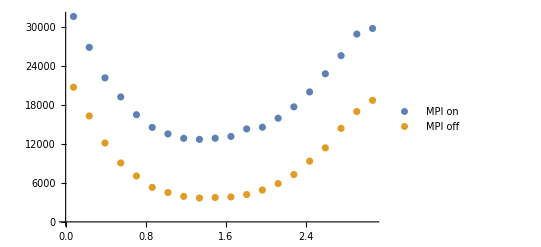

```mathematica
plot1=ListPlot[{data1MPIon, data1MPIoff},PlotLegends->{"MPI on", "MPI off"},PlotLabel->MaTeX["N=10^6, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0]"]]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr1.pdf",plot1]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr1.pdf

## [1.0, 1.4], [1.4, 2.0], N = 10^6, MPI on/off, unity

```mathematica
data2MPIonUnity=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__1014_1420_mpi_unity.csv"];
```

```mathematica
data2MPIoffUnity=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__1014_1420__unity.csv"];
```

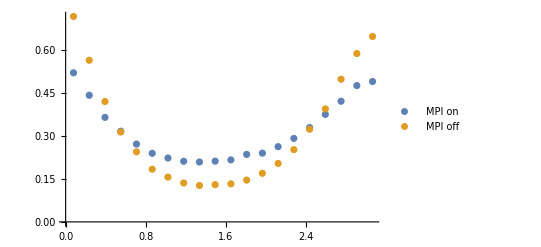

```mathematica
plot2=ListPlot[{data2MPIonUnity, data2MPIoffUnity},PlotLegends->{"MPI on", "MPI off"},PlotLabel->MaTeX["N=10^6, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\;\\int = 1"]]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf",plot2]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf

## [2.4, 2.8], [2.8, 5.0], N = 10^6

```mathematica
data2=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_2.csv"];
```

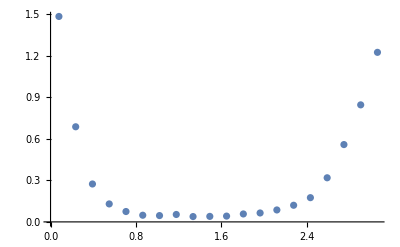

```mathematica
plot2=ListPlot[data2]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf",plot2]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf

## [1.0, 1.4], [1.4, 2.0], N = 10^7, 2.6 < η < 4.1

```mathematica
data3MPIon=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_1014_1420_mpi.csv"];
```

```mathematica
data3MPIoff=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_1014_1420__.csv"];
```

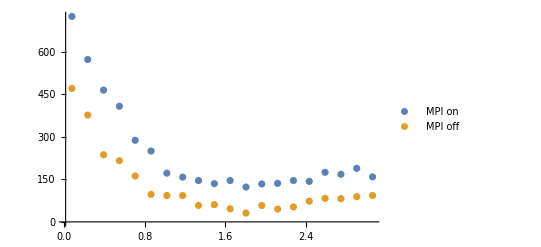

```mathematica
plot3=ListPlot[{data3MPIon, data3MPIoff},PlotLegends->{"MPI on", "MPI off"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\; y \\in [2.6, 4.1]"],PlotRange->All]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr3.pdf",plot3]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr3.pdf

## [1.0, 1.4], [1.4, 2.0], N = 10^6, 2.6 < η < 4.1

```mathematica
data4MPIon=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e8_2641_1014_1420_mpi.csv"];
```

```mathematica
data4MPIoff=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e8_2641_1014_1420__.csv"];
```

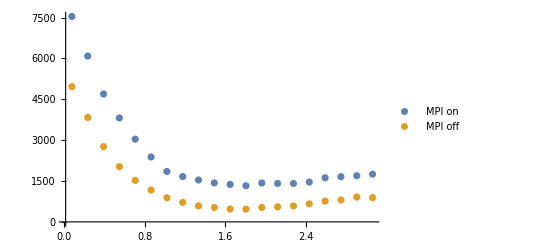

```mathematica
plot4=ListPlot[{data4MPIon,data4MPIoff},PlotLegends->{"MPI on","MPI off"},PlotLabel->MaTeX["N=10^8, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\; y \\in [2.6, 4.1]"],PlotRange->All]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr4.pdf",plot4]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr4.pdf

## [1.0, 1.4], [1.4, 2.0], N = 10^7, ensemble

```mathematica
data51=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_0010_1014_1420_mpi.csv"];
```

```mathematica
data52=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_1020_1014_1420_mpi.csv"];
```

```mathematica
data53=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2030_1014_1420_mpi.csv"];
```

```mathematica
data54=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_3040_1014_1420_mpi.csv"];
```

```mathematica
data55=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_4050_1014_1420_mpi.csv"];
```

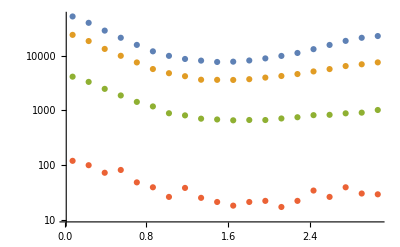

```mathematica
ListLogPlot[{data51,data52,data53,data54,data55},PlotLegends->MaTeX/@{"0.0<y<1.0","1.0<y<2.0","2.0<y<3.0","3.0<y<4.0","4.0<y<5.0"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0]"],PlotRange->All]
```

## [1.0, 1.4], [1.4, 2.0], N = 10^7, ensemble, unity

```mathematica
data61=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_0010_1014_1420_mpi_unity.csv"];
```

```mathematica
data62=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_1020_1014_1420_mpi_unity.csv"];
```

```mathematica
data63=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2030_1014_1420_mpi_unity.csv"];
```

```mathematica
data64=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_3040_1014_1420_mpi_unity.csv"];
```

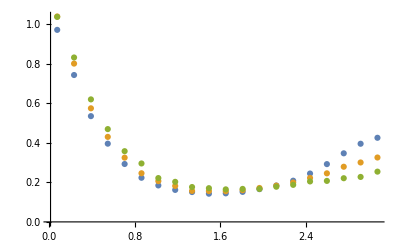

```mathematica
ListPlot[{data61,data62,data63},PlotLegends->MaTeX/@{"0.0<y<1.0","1.0<y<2.0","2.0<y<3.0","3.0<y<4.0"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\;\\int = 1"],PlotRange->All]
```

## [1.0, 1.4], [1.4, 2.0], N = 10^7, ensemble, unity

```mathematica
data71=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_5050_1014_1420_mpi_unity.csv"];
```

```mathematica
data72=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_0050_1014_1420_mpi_unity.csv"];
```

```mathematica
data73=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_1045_1014_1420_mpi_unity.csv"];
```

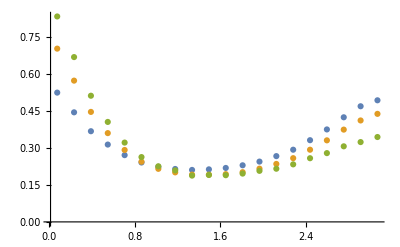

```mathematica
ListPlot[{data71,data72,data73},PlotLegends->MaTeX/@{"-5.0<y<5.0","0.0<y<5.0","1.0<y<4.5"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\;\\int = 1"],PlotRange->All]
```

## [1.0, 1.4], [1.4, 2.0], N = 10^7, ensemble, count

```mathematica
data81=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_5050_1014_1420_mpi_count.csv"];
```

```mathematica
data82=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_0050_1014_1420_mpi_count.csv"];
```

```mathematica
data83=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_1045_1014_1420_mpi_count.csv"];
```

```mathematica
data84=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_5000_1014_1420_mpi_count.csv"];
```

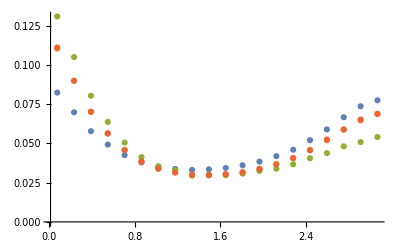

```mathematica
ListPlot[{data81,data82,data83,data84},PlotLegends->MaTeX/@{"-5.0<y<5.0","0.0<y<5.0","1.0<y<4.5","-5.0<y<0.0"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0]"],PlotRange->All]
```

## [2.4, 2.8], [2.8, 5.0], N = 10^7

```mathematica
data9=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_2428_2850_mpi_count.csv"];
```

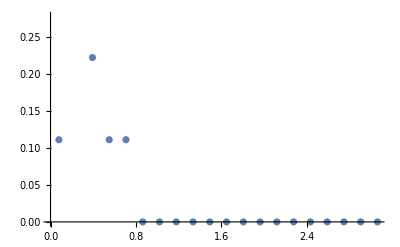

```mathematica
ListPlot[data9]
```

## [1.0, 1.4], [1.4, 2.0]; [-∞, ∞], [2.6, 4.1], N = 10^6

```mathematica
data10=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__2641_1014_1420_mpi_unity.csv"];
```

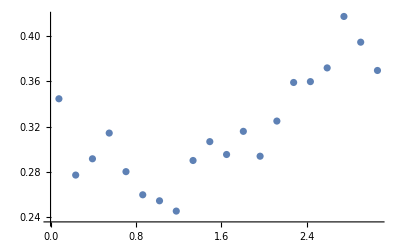

```mathematica
ListPlot[data10]
```

## [1.0, 1.4], [1.4, 2.0]; [2.6, 4.1], [2.6, 4.1], N = 10^6

```mathematica
data11=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6_2641_2641_1014_1420_mpi_unity.csv"];
```

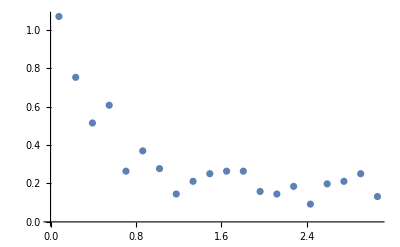

```mathematica
ListPlot[data11]
```

## [1.0, 1.4], [1.4, 2.0]; [2.6, 4.1], [2.6, 4.1], N = 10^7

```mathematica
data12=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_2641_1014_1420_mpi__.csv"];
```

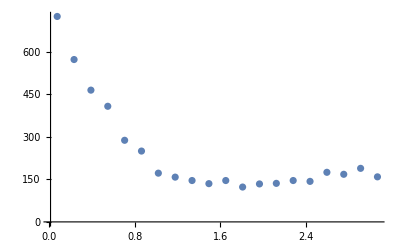

```mathematica
ListPlot[data12,PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\; y \\in [2.6, 4.1]"],PlotRange->All]
```

## [1.0, 1.4], [1.4, 2.0]; [-∞, ∞], [2.6, 4.1], N = 10^7

```mathematica
data13=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7__2641_1014_1420_mpi__.csv"];
```

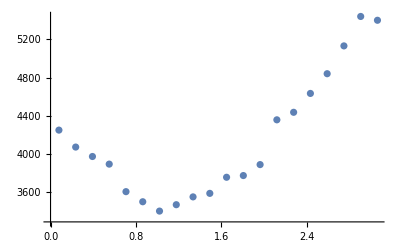

```mathematica
ListPlot[data13]
```

## [1.0, 1.4], [1.4, 2.0]; [2.6, 4.1], [-∞, ∞], N = 10^7

```mathematica
data14=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641__1014_1420_mpi__.csv"];
```

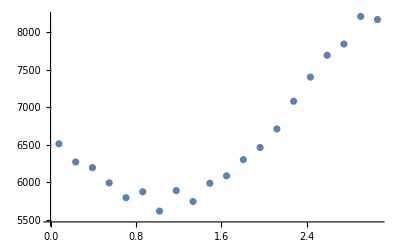

```mathematica
ListPlot[data14]
```

## [1.0, 1.4], [1.4, 2.0], N = 10^7, ensemble

```mathematica
data151=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641__1014_1420_mpi_unity.csv"];
```

```mathematica
data152=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_5050_1014_1420_mpi_unity.csv"];
```

```mathematica
data153=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_0050_1014_1420_mpi_unity.csv"];
```

```mathematica
data154=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_1045_1014_1420_mpi_unity.csv"];
```

```mathematica
data155=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_2641_1014_1420_mpi_unity.csv"];
```

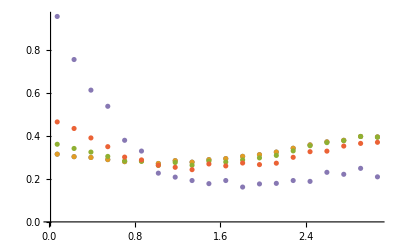

```mathematica
plot5=ListPlot[{data151,data152,data153,data154,data155},PlotLegends->MaTeX/@{"-\\infty<y_2<\\infty","-5.0<y_2<5.0","0.0<y_2<5.0","1.0<y_2<4.5","2.6<y_2<4.1"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\; y_1\\in [2.6, 4.1]"],PlotRange->All]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/birap1.pdf",plot5]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/birap1.pdf

## [1.0, 1.4], [1.4, 2.0], N = 10^7, ensemble

```mathematica
data161=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641__1014_1420_mpi__.csv"];
```

```mathematica
data162=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_2641c_1014_1420_mpi__.csv"];
```

```mathematica
data163=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_2641_1014_1420_mpi__.csv"];
```

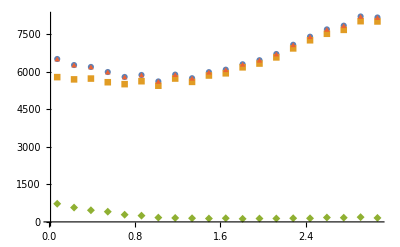

```mathematica
plot6=ListPlot[{data161,data162,data163,Transpose[{data162[[All,1]],data162[[All,2]]+data163[[All,2]]}]},PlotLegends->MaTeX/@{"y_2\\in \\left]-\\infty,\\infty\\right[","y_2\\notin [2.6, 4.1]","y_2\\in [2.6, 4.1]","\\Sigma"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\; y_1\\in [2.6, 4.1]"],PlotRange->All,PlotMarkers->{Automatic,Automatic,Automatic,{Automatic,0.02}}]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/birap2.pdf",plot6]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/birap2.pdf